# Polypool: Studying infinitely bouncing cue balls in polygons

## Abstract

In this computational essay, I investigated what happened when a cue ball bounced around the interior of a polygon for an arbitrary number of bounces. The goal was to discover patterns in the distribution of the coverings created by these processes. This data was then combined with image processing techniques to extract insights about these coverings and the effect of initial conditions on them.

## 1. Introduction

The polypool process began with a programming method of generating polygons. Initial tests were ran on random polygons, though as I progressed it became rhombi, as rhombi are relatively simple geometrically. In order to implement a bouncing ball, I decided on using a raycasting algorithm (which is elaborated on in depth later) to “bounce” the ball iteratively hundreds or thousands of times. Once we have a plot of those bounces, we can use the image data to gain useful information.

This project was motivated by a simple little theorem from measure theory: given a bouncing ball in a square, we can

While each section will go more into more detail, I’ll elaborate on the concepts of raycasting here first. Raycasting is an algorithm that originates in 3D computer graphics. The idea is to take a large number of rays and “cast” them at a scene, find where they intersect parts of that scene, and then generate an image based on that. For this project we have the sides of a polygon instead of a scene and a bouncing point instead of a pixel.

In Chapter 2 we will examine what happens when this procedure is done in rhombi, squares, and randomly generated n-gons. The image data is then used to plot a probability distribution of the data based on the intensity of each pixel in our polygons.

## Part One: Polygons

### Initialization

The first task in making Polypool simulations is setting up a bunch of data. For our rhomboids, all we need is a length and two angles. For more complex shapes, we would need hyper-complex parameterizations, so we randomly generate them instead.

Take an angle and generate a unit rhombus:

```mathematica
genRhombus[angle_]:= CanonicalizePolygon[Parallelogram[{0,0},{{1,0},AngleVector[angle]}]]
```

### Utility Functions

Raycasting is fundamentally a geometric algorithm. To that end, there’s a lot of basic geometric computation that needed to be done to implement this. The following functions are all utilities that are necessary to make the main ray algorithm work.

sideList takes the boundary of a polygon and finds the list of Line objects that make up the edges of that polygon from its boundary:

```mathematica
sideList[poly0_] := Module[{poly = poly0},Line /@ Partition[#,2,1]& @ Partition[#,2]& @ (Flatten @ (List @@ RegionBoundary[poly]))]
```

This function converts a point in a polygon to the edge of the polygon it resides on:

```mathematica
getCurrentSide[poly_,point_] := Extract[#,{1}]& @ First @ SortBy[RegionDistance[#,point]&] @ sideList[poly]
```

This function converts an array of coordinate pairs to a component form vector, which is necessary for computing collisions later on:

```mathematica
lineToVecRep[line_] := line[[2]]-line[[1]]
```

This function takes a vector and a pair of coordinate pairs (representing a line) and creates a new vector representing the path of a ball after hitting the side (See Acknowledgements):

```mathematica
calculateNewDirection[originVector_, sideVec_]:=Normalize[(2*Projection[originVector,sideVec])-originVector]
```

calculateIntersection takes a ray and a line segment and computes the point where they intersect (this is the core of the raycast algorithm, see Acknowledgements):

```mathematica
calculateIntersection[ray_, segment_] :=
Module[ {
rx =ray[[1]][[1]],
ry = ray[[1]][[2]],
rdx = ray[[2]][[1]],
rdy = ray[[2]][[2]],
startx = segment[[1]][[1]], 
starty = segment[[1]][[2]], 
endx= segment[[2]][[1]], 
endy = segment[[2]][[2]]},
Quiet @ Solve[t {startx, starty} + (1 - t) {endx, endy} =={rx, ry} + u {rdx, rdy}, {t, u},
Assumptions->0 <= t <= 1 && u > 0
]
]
```

## 2. Pool and Pretty Pictures

## Part Two: The Main Raycasting Algorithm

This section discusses the “main algorithm” that I referred to earlier. It is implemented in a few functions, notably castRayPolygon and castRayPolygonNestable and their quadrilateral . These functions take an abstract representation of a ray and figure out where it will collide with the polygon again. This can be naively iterated over to compute many raycasts, though it is very slow, so castRayPolygonNestable allows the algorithm to be executed in accordance with the functional paradigm and Wolfram Kernel’s optimizations. This section contains two sets of raycasting algorithms. These are castRayPolygon and castRayQuad, and their corresponding nest wrappers. The reason for this is simply that the numerical algorithm used in castRayQuad did not work on general polygons, and vise versa. These functions synthesize all of the previous utilities and data to produce arbitrarily iterated raycasts.

### Raycasting Implementations

#### detectCollision

The collision detection subroutine used by all the other raycasting algorithms:

```mathematica
detectCollision[ray_,sides_] := Module[{possibleCollisions,dist,pointOfCollision,direction},
direction = ray[[2]];
possibleCollisions =   calculateIntersection[ray,#]&  /@ (Sequence @@@sides);
dist = Max @ ((Flatten @ (u /. (possibleCollisions))) /.  u-> -Infinity);
ray[[1]] + (dist *direction)
]
```

This function is fundamental to raycasting. Using an intersection point from Next we have the three casting functions, castRayQuad, castRayPolygon, and generateInitialCast. These all use the same underlying raycasting concepts I’ve discussed throughout this whole essay, but are slightly different.

#### castRayQuad

castRayQuad is a function that takes a quadrilateral, a point, and a vector. point represents a point on one line of the polygon and originVector represents the direction of the ray that got us to that point.

```mathematica
castRayQuad[quad_, point_,originVector_] := Module[{currentSide,ray,sides,collisions,dist,newDirection,possibleCollisions,pointOfCollision},
sides = sideList[quad];
currentSide = getCurrentSide[quad,point];
newDirection = calculateNewDirection[originVector,lineToVecRep[currentSide]];
ray = HalfLine[point,newDirection];
pointOfCollision = detectCollision[ray,sides];
{pointOfCollision, point,newDirection}
]
```

#### castRayPolygon

castRayPolygon is a slightly different version of the above function that works in general polygons. Otherwise, it works the same way.

```mathematica
castRayPolygon[poly_, point_,originVector_] := Module[{currentSide,ray,sides,collisions,pointOfCollision,oppRay,newDirection,possibleCollisions},
sides = sideList[poly];
currentSide = getCurrentSide[poly,point];
newDirection = calculateNewDirection[originVector,lineToVecRep[currentSide]];
ray = HalfLine[point,newDirection];
possibleCollisions =   (List @@ RegionIntersection[ray,RegionBoundary@ poly])[[1]];
pointOfCollision = Last @ (SortBy[EuclideanDistance[#,point]&][possibleCollisions]);
collisionSide = Extract[#,{1}]& @ Last @ SortBy[sides, RegionDistance[#,pointOfCollision]&];
Return @ {pointOfCollision, currentSide,point,newDirection};
];
```

#### generateInitialCast

This function ties together all the initial conditions we set in Part One to “kick off” the actual raycasting. It accompanies castRayQuad to allow us to set very specific initial conditions for our raycasts.

Cast a ray at a given angle at a certain length along one side of a polygon:

```mathematica
generateInitialCast[quad_, angle_,length_] := Module[{sides,ray,possibleCollisions,dist,pointOfCollision,direction,startPoint},
sides = sideList @ quad;
startPoint = {sides[[1]][[1]][[1]][[1]]+length,0};
direction = AngleVector[angle];
ray = HalfLine[startPoint, direction];
pointOfCollision = detectCollision[ray,sides];
{pointOfCollision,pointOfCollision-startPoint}
]
```

#### castRayPolygonNestable

This function, while important, is much simpler than castRayPolygon because it just abstracts the logic away from the previous function. It works with either the polygon or quadrilateral versions.

Allows the raycasting algorithm to be Nested:

```mathematica
castRayPolygonNestable[poly_, {point_,originVector_}] := 
	castRayPolygon[poly,point,originVector][[{1,4}]]
```

```mathematica
castRayQuadNestable[poly_, {point_,originVector_}] := 
	castRayQuad[poly,point,originVector][[{1,3}]]
```

### And Finally...

We now have the utility to actually begin bouncing some cueballs. In this example, we will use a rhombus. Rhombi are interesting shapes to use as pool tables because while they are geometrically and algebraically simple, they create interesting lattice pattern that make them good test shapes. The following block of code-text walks through the raycast algorithm on a rhombus. Later on, this will be modularized and expanded into a succinct function block.

Initializes an empty list of points:

```mathematica
points = {};
```

Creates data to represent our initial conditions:

```mathematica
quad = genRhombus[Pi/4];
initialAngle = Pi/6;
initialLength = 0.5;
```

This takes our rhombus and a choice of initial angle and length along the rhombus edge:

```mathematica
{breakPoint,startDirection} = generateInitialCast[quad, initialAngle,initialLength];
```

Plots first raycast and sets up the points list:

```mathematica
castInfo = castRayQuad[quad, breakPoint, startDirection];
AppendTo[points,castInfo[[1]]];
```

Iterates the raycast 1,000 times:

```mathematica
Nest[(c = castRayQuadNestable[quad,#];AppendTo[points,c[[1]]];c)&,{breakPoint,startDirection},1000];
```

Splits the points into overlapping pairs representing line segments:

```mathematica
individualLines = Line /@ Partition[points, 2, 1];
```

Displays the resulting lines as an image:

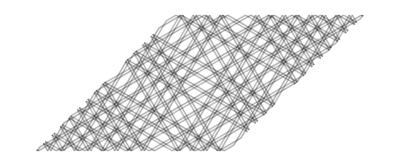

```mathematica
rayPainting =Style[Graphics[{Opacity[0.05],individualLines}],Antialiasing->False]
```

### Image Processing 101

As you can see, we can get interesting patterns from even the humble rhombus. We will now quantify what interesting means through some convenient image processing. This manifests in two forms: histograms and transforms. The histogram is a very simple process. First, we take the image data of a raycast and convert it to grayscale. Once we have pure grayscale data, we need to take the logarithm. This happens because of the way we drew images in the previous section. To draw pixels that get darker where more rays intersect, we use Opacity. However, in image processing, opacity is a mulitplicative value, not additive. This means that every time a ray crosses another ray, their color values are scaled, not added together. To undo this exponential effect, we take the logarithm. Once we have all that data, it can be very easily plotted onto a histogram as below. Our last image processing technique was a later addition. One other way of analyzing density is by examining the magnitude of the Fourier transform of an image. Areas in the FT diagrams with more red represents cross sections of the image with higher intensity and vise versa.

Rasterizes the raycast image to get pixel data:

```mathematica
raster = Rasterize @ rayPainting;
```

Takes the logarithm and negates the grayscale values of the raster:

```mathematica
data = -1*#& @Select[Flatten @Log @ ImageData @ ColorConvert[raster, "Grayscale"],#!=0&];
```

Plots the resulting data as text:

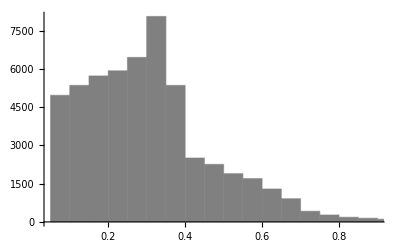

```mathematica
hist = Histogram[data,Automatic,"Count",ChartStyle->Gray]
```

Create the magnitude diagram of the Fourier transform of the image data:

```mathematica
Abs[Fourier[ImageData[Rasterize@rayPainting]]]//Image
```

-Graphics-

## Part Three: General N-gons

### Modularization

Now that we have a method to generate raycasts in a rhombus, we can generalize. The first step in doing this is creating a function that does all of that work in one cell. The result is fullRaycastX, which  computes the entire initialization, casting, rendering, and analysis process at once. As with the basic casting functions, there’s one for basic rhombi (labelled with quad) and one for other polygons (labelled with poly).

```mathematica
fullRaycastQuad[quad_, initialAngle0_, initialLength0_] := Module[{points,breakPoint,startDirection,castInfo,rayPainting,data,hist,raster,angle=initialAngle0,length=initialLength0,individualLines},
points = {};
{breakPoint,startDirection} = generateInitialCast[quad, angle,length];
castInfo = castRayQuad[quad, breakPoint, startDirection];
AppendTo[points,castInfo[[1]]];
Nest[(c = castRayQuadNestable[quad,#];AppendTo[points,c[[1]]];c)&,{breakPoint,startDirection},1000];
individualLines = Line /@ Partition[points, 2, 1];
rayPainting =Style[Graphics[{Opacity[0.05],individualLines}],Antialiasing->False];
raster = Rasterize @ rayPainting;
data = -1*#& @Select[Flatten @Log @ ImageData @ ColorConvert[raster, "Grayscale"],#!=0&];
hist = Histogram[data,Automatic,"Count",ChartStyle->Gray];
{raster, hist}
];
```

We will now “show off” our new raycast generator by computing raycasts in a very thin rhombus:

Compute raycast data in a very thin rhombus:

```mathematica
cst = fullRaycastQuad[genRhombus[Pi/28],Pi/6, 0.5];
```

```mathematica
Show[cst[[1]]]
```

-Graphics-

Along with the polygon itself, we can also analyze the Fourier transforms and histograms:

```mathematica
Abs[Fourier[ImageData[cst[[1]]]]]//Image
```

-Graphics-

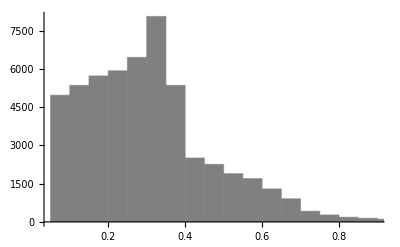

```mathematica
Show[cst[[2]]]
```

As discussed earlier, we have a version of the full cast algorithm for general polygons with random conditions:

```mathematica
fullRaycastPoly[poly_] := Module[{boundary, initialDirection,casts, rays, centroid,points,breakPoint,castInfo,rayPainting,data,hist,raster},
boundary = RegionBoundary @ poly;
centroid = RegionCentroid @ poly;
breakPoint = RandomPoint @ boundary;
initialDirection = breakPoint - centroid;
rays = {};
AppendTo[rays, Line[{breakPoint,centroid}]];
castInfo = castRayPolygon[poly, breakPoint, breakPoint-centroid];
AppendTo[rays,Line[{castInfo[[3]],castInfo[[1]]}]];
casts = Reap @ Nest[Sow[castRayPolygonNestable[poly,#]]&,{breakPoint,breakPoint-centroid},1000];
AppendTo[rays, Line /@ Partition[(Transpose @ casts[[2]][[1]] )[[1]],2,1]];
rayPainting = Graphics[{Opacity[0.05],rays}];
raster = Rasterize @ rayPainting;
data = -1*#& @Select[Flatten @Log @ ImageData @ ColorConvert[raster, "Grayscale"],#!=0&];
hist = Histogram[data,Automatic,"Count",ChartStyle->Gray];
{raster,hist}
];
```

As with rhombi, we can display the same sort of data. Notice that random polygons have a much greater variety in distributions and transforms.

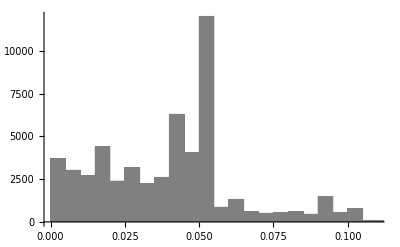
{-Graphics-,-Graphics-}

```mathematica
cstOnPoly = fullRaycastPoly[RandomPolygon[7]];
```

```mathematica
cstOnPoly[[1]]
```

-Graphics-

```mathematica
Abs[Fourier[ImageData[cstOnPoly[[1]]]]]//Image
```

-Graphics-

```mathematica
Show[cstOnPoly[[2]]]
```

-Graphics-

## 3. Conclusions

As we can see, this algorithm can produce a huge variety of results in a wide array of possible polygons. Given even more computing power and higher resolution images, further conclusions could be drawn. Of course, could be explored more rigorously using pure mathematics and analysis, though that is out of the scope of this essay. Further directions include more optimizations of this algorithm and a more unified codebase (less fragmentation between classes of polygons) and better analysis of raycast data.

## References

1 . William, Simon Woods, & Matthias Odisio. (2013, June 1). Getting RGBA data from an image. Mathematica Stack Exchange. https://mathematica.stackexchange.com/questions/26770/getting-rgba-data-from-an-image 

2 . Points, lines, and planes. Point, Line, Plane. (n.d.). https://paulbourke.net/geometry/pointlineplane/ 

3. Developers of Matlab. (n.d.). Fourier Transform. MathWorks. https://www.mathworks.com/help/images/fourier-transform.html 

4. Users of Mathematica Stack Exchange. (1959, February 1). Calculate the 2d Fourier transform of an image. Mathematica Stack Exchange. https://mathematica.stackexchange.com/questions/29203/calculate-the-2d-fourier-transform-of-an-image

## Acknowledgements

I’d like to thank my wonderful mentor Dr. Lyman Hurd for all his assistance with mathematics, program implementations, code reviews, and putting up with my insanity for 7 hours a day. I’d also like to thank program faculty Dugan Hammock for assistance with writing the intersection algorithms and fellow program student Christopher Gilbert for mathematical assistance with the ray direction calculations. Finally, I’d like to thank my group mate Max Niederman and program directors Eryn and Megan for being sources of endless helpful distractions during many a stressful coding session.